### Chapter VII Creating Interactive Models

#### Manipulate

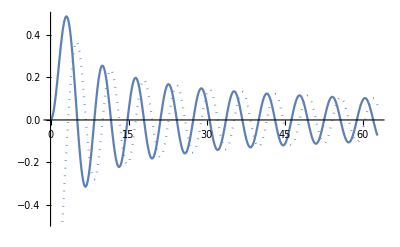

```mathematica
ReImPlot[HankelH1[2,x],{x,0,20π}]
```

#### Manipulate needs to specify the parameters

```mathematica
Manipulate[ReImPlot[HankelH1[n,k x],{x,0,20π}],{n,1,5},{k,1,2}]
```

#### It can be used to give a list of discrete choices

```mathematica
Manipulate[ReImPlot[function[n,k x],{x,Llim,Rlim}],{n,1,5},{k,1,2},{Llim,0,1},{Rlim,2π,20π},{function,{HankelH1,HankelH2}}]
```

#### Manipulating can also create discrete parameters

```mathematica
Manipulate[Expand[(a+b)^n],{n,2,10,1},ControlType->PopupMenu]
```

The label of the parameters and the plot can be modified and updated automatically, double-click the result cell to hide code
Initial values can also be specified

```mathematica
Manipulate[Plot3D[Sin[k x+n y]+Cos[n y],{y,-1,1},{x,-1,1},PlotLabel->"Sin("<>ToString[k]<>"x+"<>ToString[n]<>"y)+Cos("<>ToString[n]<>"y)"],{{k,2,"X Frequency"},0,10},{{n,1,"Y Frequency"},0,10}]
```

#### Using user defined functions

```mathematica
Manipulate[Plot[Function[a x^2+b x+c][x],{x,-4,4}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

Or use Initialization to define function within Manipulate

```mathematica
Manipulate[Plot[f[a*x],{x,-π,π},PlotRange->{-1,1}],{a,-1,1},Initialization:>(f[x_]:=Sin[2 x^2+2x+1]),SaveDefinitions->True]
```

```mathematica
Clear[f]
```